#### Attempt 1 (book’s result)

```mathematica
Series[1-n-(1-n+theta^2/2)omegap^2/omega^2 gamma^-3(1-n+1/2 (theta^2+gamma^-2))^-2/.gamma-> 1/x,{theta,0,2},{x,0,3}]
```

((1-n)+(omegap^2 x^3)/((-1+n) omega^2)+O[x]^4)+((omegap^2 x^3)/(2 (-1+n)^2 omega^2)+O[x]^4) theta^2+O[theta]^3

```mathematica
Solve[(1-n)+(omegap^2 x^3)/((-1+n) omega^2)==0,n]
```

{{n→(omega-omegap x^(3/2))/omega},{n→(omega+omegap x^(3/2))/omega}}

#### Attempt 2 (Andrea’s result?)

```mathematica
Series[1-n-(1-n+theta^2/2)omegap^2/omega^2 gamma^-3(1/2 (theta^2+gamma^-2))^-2/.gamma-> 1/x,{theta,0,2},{x,0,3}]
```

((-(4 omegap^2)/omega^2+(4 n omegap^2)/omega^2)/x+(1-n)+O[x]^4)+(((8 omegap^2)/omega^2-(8 n omegap^2)/omega^2)/x^3-(2 omegap^2)/(omega^2 x)+O[x]^4) theta^2+O[theta]^3

#### Attempt 3 (closest to Pani’s result - look here!)

```mathematica
Series[n/.Solve[1-n(*-*)+(1-n+theta^2/2)omegap^2/omega^2 gamma^-3(1/2 (theta^2+gamma^-2))^-2==0,n]/.gamma-> omega^2 Ap/omegap^2,{theta,0,2},{Ap,0,3}]//Simplify
```

{1+(2 Ap-8 Ap^2+32 Ap^3+O[Ap]^4) theta^2+O[theta]^3}

```mathematica
Series[1-n-(1-n+theta^2/2)omegap^2/omega^2 gamma^-3(1-n+1/2 (theta^2+gamma^-2))^-2/.gamma-> omega^2 Ap/omegap^2,{theta,0,2},{Ap,0,1}]
```

((1-n)+(-4+4 n) Ap+O[Ap]^2)+(-2 Ap+O[Ap]^2) theta^2+O[theta]^3

```mathematica
Series[n/.Solve[(1-n)+(-4+4 n) Ap+(-2 Ap)theta^2==0,n],{theta,0,2},{Ap,0,1}]
```

{1+(-2 Ap+O[Ap]^2) theta^2+O[theta]^3}

```mathematica
Series[1-n-(1-n+theta^2/2)omegap^2/omega^2 gamma^-3((*1-n*)+1/2 ((*theta^2*)+gamma^-2))^-2/.gamma-> omega^2 Ap/omegap^2,(*{theta,0,2},*){Ap,0,1}]
```

(1-n)+(-4+4 n-2 theta^2) Ap+O[Ap]^2

```mathematica
Series[n/.Solve[(1-n)+(-4+4 n-2 theta^2) Ap==0,n],(*{theta,0,2},*){Ap,0,1}]//Simplify
```

{1-2 theta^2 Ap+O[Ap]^2}

#### The three solutions

```mathematica
Series[n/.nsols⟦3⟧,{theta,0,2},{Ap,0,1},Assumptions->{omega>0, omegap>0,Ap>0}]
```

(omegap^4/(2 omega^4 Ap^2)-omegap^4/(omega^4 Ap^(3/2))+1+O[Ap]^(3/2))+(1/2+(√Ap)/2+Ap+O[Ap]^(3/2)) theta^2+O[theta]^3

```mathematica
Series[n/.nsols⟦2⟧,{theta,0,2},{Ap,0,1},Assumptions->{omega>0, omegap>0,Ap>0}]
```

(omegap^4/(2 omega^4 Ap^2)+omegap^4/(omega^4 Ap^(3/2))+1+O[Ap]^(3/2))+(1/2-(√Ap)/2+Ap+O[Ap]^(3/2)) theta^2+O[theta]^3

```mathematica
Series[n/.nsols⟦1⟧,{theta,0,2},{Ap,0,1},Assumptions->{omega>0, omegap>0,Ap>0}]
```

(1+O[Ap]^(3/2))+(-2 Ap+O[Ap]^(3/2)) theta^2+O[theta]^3

```mathematica
nsols=Solve[1-n-(1-n+theta^2/2)omegap^2/omega^2 gamma^-3(1-n+1/2 (theta^2+gamma^-2))^-2==0//.gamma-> omega^2 Ap/omegap^2,n]//Simplify;
```

```mathematica
Dimensions[nsols]
```

{3,1}

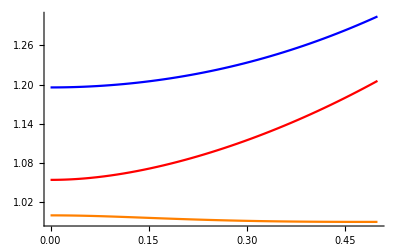

```mathematica
Show[Plot[Evaluate[n/.nsols⟦2⟧]//.gamma-> 2//.omega-> 5//.omegap-> 1,{theta,0,0.5},PlotStyle->{Blue},PlotRange->All,AxesOrigin->{0,0}],Plot[Evaluate[n/.nsols⟦3⟧]//.gamma-> 2//.omega-> 5//.omegap-> 1,{theta,0,0.5},PlotStyle->{Red}],Plot[Evaluate[n/.nsols⟦1⟧]//.gamma-> 2//.omega-> 5//.omegap-> 1,{theta,0,0.5},PlotStyle->{Orange}]]
```

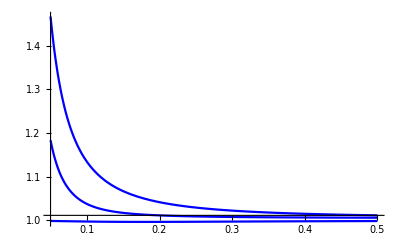

```mathematica
Show[Plot[Evaluate[n/.nsols⟦2⟧]//.gamma-> omega^2 Ap/omegap^2//.omega-> 5//.omegap-> 1/.theta-> 0.1,{Ap,0.05,0.5},PlotStyle->{Blue},PlotRange->All],Plot[Evaluate[n/.nsols⟦3⟧]//.gamma-> omega^2 Ap/omegap^2//.omega-> 5//.omegap-> 1/.theta-> 0.1,{Ap,0.05,0.5},PlotStyle->{Blue},PlotRange->All,AxesOrigin->{0,0}],Plot[Evaluate[n/.nsols⟦1⟧]//.gamma-> omega^2 Ap/omegap^2//.omega-> 5//.omegap-> 1/.theta-> 0.1,{Ap,0.05,0.5},PlotStyle->{Blue},PlotRange->All,AxesOrigin->{0,0}]]
```

#### theta average

```mathematica
Integrate[gamma^-3(1-n+1/2 (theta^2+gamma^-2))^-2,{theta,0,π}]
```

ConditionalExpression[4 gamma (π/(2 (1-2 gamma^2 (-1+n)) (1+gamma^2 (2-2 n+π^2)))+ArcTan[(gamma π)/(√(1-2 gamma^2 (-1+n)))]/(2 gamma (1-2 gamma^2 (-1+n))^(3/2))),(Re[(√(-1+2 gamma^2 (-1+n)))/gamma]>π||(√(-1+2 gamma^2 (-1+n)))/gamma∉ℝ||π+Re[(√(-1+2 gamma^2 (-1+n)))/gamma]<0)&&(Im[(√(1-2 gamma^2 (-1+n)))/gamma]>π||π+Im[(√(1-2 gamma^2 (-1+n)))/gamma]<0||Re[(√(1-2 gamma^2 (-1+n)))/gamma]≠0)]

```mathematica
aver=4 gamma (π/(2 (1-2 gamma^2 (-1+n)) (1+gamma^2 (2-2 n+π^2)))+ArcTan[(gamma π)/(√(1-2 gamma^2 (-1+n)))]/(2 gamma (1-2 gamma^2 (-1+n))^(3/2)))
```

4 gamma (π/(2 (1-2 gamma^2 (-1+n)) (1+gamma^2 (2-2 n+π^2)))+ArcTan[(gamma π)/(√(1-2 gamma^2 (-1+n)))]/(2 gamma (1-2 gamma^2 (-1+n))^(3/2)))

```mathematica
aver/.gamma-> 1/x//Simplify
```

(2 ((π x^4)/((2-2 n+x^2) (2-2 n+π^2+x^2))+(x ArcTan[π/(√(1+(2-2 n)/x^2) x)])/(((2-2 n+x^2)/x^2)^(3/2))))/x

```mathematica
(Series[aver/.gamma-> 1/x,{x,0,3}])
```

-(π x^3)/((-1+n) (2-2 n+π^2))+O[x]^4

```mathematica
-(π x^3)/((-1+n) (2-2 n+π^2))/.x-> 1/gamma//Simplify
```

-π/(gamma^3 (-1+n) (2-2 n+π^2))

```mathematica
Eq=1-n-(1-n+theta^2/2)omegap^2/omega^2(-π/(gamma^3 (-1+n) (2-2 n+π^2)))//Simplify
```

1-n+(omegap^2 π (2-2 n+theta^2))/(2 gamma^3 (-1+n) omega^2 (2-2 n+π^2))

```mathematica
Series[n/.Solve[Eq==0,n]//Simplify,{theta,0,2}]
```

{1/(48 gamma^3 omega^2)(8 gamma^3 omega^2 (6+π^2)-(8 π^(2/3) (6 gamma^3 omega^2 omegap^2+gamma^6 omega^4 π^3))/(-9 gamma^6 omega^4 omegap^2 π^2-gamma^9 omega^6 π^5+3 √(3 π) √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)))^(1/3)-8 π^(1/3) (-9 gamma^6 omega^4 omegap^2 π^2-gamma^9 omega^6 π^5+3 √(3 π) √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)))^(1/3))+1/(48 gamma^3 omega^2)((8 gamma^9 omega^6 (6 omegap^2+gamma^3 omega^2 π^3) (-9 √3 gamma^6 omega^4 omegap^4 π^(3/2)-√3 gamma^9 omega^6 omegap^2 π^(9/2)+9 omegap^2 √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3))))/(√(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)) (-9 gamma^6 omega^4 omegap^2 π^(3/2)-gamma^9 omega^6 π^(9/2)+3 √3 √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)))^(4/3))-(8 (-9 √3 gamma^12 omega^8 omegap^4 π^(3/2)-√3 gamma^15 omega^10 omegap^2 π^(9/2)+9 gamma^6 omega^4 omegap^2 √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3))))/(√(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)) (-9 gamma^6 omega^4 omegap^2 π^(3/2)-gamma^9 omega^6 π^(9/2)+3 √3 √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)))^(2/3))) theta^2+O[theta]^3,1/(96 gamma^3 omega^2)(16 gamma^3 omega^2 (6+π^2)+(8 (1+ⅈ √3) π^(2/3) (6 gamma^3 omega^2 omegap^2+gamma^6 omega^4 π^3))/(-9 gamma^6 omega^4 omegap^2 π^2-gamma^9 omega^6 π^5+3 √(3 π) √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)))^(1/3)+8 (1-ⅈ √3) π^(1/3) (-9 gamma^6 omega^4 omegap^2 π^2-gamma^9 omega^6 π^5+3 √(3 π) √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)))^(1/3))+1/(96 gamma^3 omega^2)((8 (1+ⅈ √3) gamma^9 omega^6 (6 omegap^2+gamma^3 omega^2 π^3) (9 √3 gamma^6 omega^4 omegap^4 π^(3/2)+√3 gamma^9 omega^6 omegap^2 π^(9/2)-9 omegap^2 √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3))))/(√(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)) (-9 gamma^6 omega^4 omegap^2 π^(3/2)-gamma^9 omega^6 π^(9/2)+3 √3 √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)))^(4/3))+(8 ⅈ (ⅈ+√3) (9 √3 gamma^12 omega^8 omegap^4 π^(3/2)+√3 gamma^15 omega^10 omegap^2 π^(9/2)-9 gamma^6 omega^4 omegap^2 √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3))))/(√(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)) (-9 gamma^6 omega^4 omegap^2 π^(3/2)-gamma^9 omega^6 π^(9/2)+3 √3 √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)))^(2/3))) theta^2+O[theta]^3,1/(96 gamma^3 omega^2)(16 gamma^3 omega^2 (6+π^2)+(8 (1-ⅈ √3) π^(2/3) (6 gamma^3 omega^2 omegap^2+gamma^6 omega^4 π^3))/(-9 gamma^6 omega^4 omegap^2 π^2-gamma^9 omega^6 π^5+3 √(3 π) √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)))^(1/3)+8 (1+ⅈ √3) π^(1/3) (-9 gamma^6 omega^4 omegap^2 π^2-gamma^9 omega^6 π^5+3 √(3 π) √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)))^(1/3))+1/(96 gamma^3 omega^2)((8 (1-ⅈ √3) gamma^9 omega^6 (6 omegap^2+gamma^3 omega^2 π^3) (9 √3 gamma^6 omega^4 omegap^4 π^(3/2)+√3 gamma^9 omega^6 omegap^2 π^(9/2)-9 omegap^2 √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3))))/(√(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)) (-9 gamma^6 omega^4 omegap^2 π^(3/2)-gamma^9 omega^6 π^(9/2)+3 √3 √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)))^(4/3))-(8 ⅈ (-ⅈ+√3) (9 √3 gamma^12 omega^8 omegap^4 π^(3/2)+√3 gamma^15 omega^10 omegap^2 π^(9/2)-9 gamma^6 omega^4 omegap^2 √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3))))/(√(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)) (-9 gamma^6 omega^4 omegap^2 π^(3/2)-gamma^9 omega^6 π^(9/2)+3 √3 √(-gamma^9 omega^6 omegap^4 (8 omegap^2+gamma^3 omega^2 π^3)))^(2/3))) theta^2+O[theta]^3}